ResourceFunction["MaTeXInstall"][]

```mathematica
<<MaTeX`
```

```mathematica
TempArray={0.01,0.015,0.02,0.025,0.03,0.035,0.04,0.045,0.05,0.055,0.06,0.065,0.07,0.075,0.08,0.085}
```

{0.01,0.015,0.02,0.025,0.03,0.035,0.04,0.045,0.05,0.055,0.06,0.065,0.07,0.075,0.08,0.085}

```mathematica
Tc=0.082
```

0.082

```mathematica
FreeEnergyA ={-26.2181,-26.3131,-26.49322,-26.7577,-27.094,-27.5025,-27.96914,-28.4772,-29.03713,-29.64513,-30.30158,-31.01845,-31.7946,-32.62281,-33.49871,-34.41945};
```

```mathematica
FreeEnergyB = {-26.0661,-26.21506,-26.41247,-26.68474,-27.01344,-27.40712,-27.86103,-28.38201,-28.95543,-29.5925,-30.27327,-31.01902,-31.79555,-32.62794,-33.49909,-34.41489};
```

```mathematica
deltaFA =( FreeEnergyA-FreeEnergyB)
```

{-0.152,-0.09804,-0.08075,-0.07296,-0.08056,-0.09538,-0.10811,-0.09519,-0.0817,-0.05263,-0.02831,0.00057,0.00095,0.00513,0.00038,-0.00456}

```mathematica
AvgCurvatureA ={11.95,11.97,12.03,12.15,12.28,12.4,12.49,12.53,12.56,12.55,12.53,12.5,12.44,12.33,12.2,12.07};
```

```mathematica
AvgCurvatureB={13.77,13.74,13.67,13.6,13.51,13.4,13.27,13.15,13.02,12.88,12.74,12.61,12.47,12.33,12.2,12.07};
```

```mathematica
alphaArray = AvgCurvatureA/AvgCurvatureB
```

{0.867829,0.871179,0.880029,0.893382,0.908956,0.925373,0.941221,0.952852,0.96467,0.974379,0.983516,0.991277,0.997594,1.,1.,1.}

```mathematica
betaArray = 1/TempArray;
```

```mathematica
Exp[-betaArray*deltaFA]
```

{3.99279×10^6,689.523,56.6845,18.5116,14.6631,15.2586,14.9207,8.29235,5.12433,2.60364,1.60293,0.991269,0.98652,0.933887,0.995261,1.05511}

```mathematica
curvxx =Table[(1+Exp[-betaArray[[n]]*deltaFA[[n]]])/(AvgCurvatureB[[n]]+AvgCurvatureA[[n]]Exp[-betaArray[[n]]*deltaFA[[n]]]),{n,1,Dimensions[TempArray][[1]]}]
```

{0.083682,0.0835243,0.0829295,0.0818042,0.0809158,0.0802471,0.0797512,0.0793857,0.0791445,0.0791041,0.0792979,0.079648,0.0802884,0.081103,0.0819672,0.08285}

```mathematica
curvxxGS=Table[1/AvgCurvatureA[[n]],{n,1,Dimensions[TempArray][[1]]}]
```

{0.083682,0.0835422,0.0831255,0.0823045,0.0814332,0.0806452,0.0800641,0.0798085,0.0796178,0.0796813,0.0798085,0.08,0.0803859,0.081103,0.0819672,0.08285}

```mathematica
curvxxES=Table[1/AvgCurvatureA[[n]],{n,1,Dimensions[TempArray][[1]]}]
```

{0.083682,0.0835422,0.0831255,0.0823045,0.0814332,0.0806452,0.0800641,0.0798085,0.0796178,0.0796813,0.0798085,0.08,0.0803859,0.081103,0.0819672,0.08285}

```mathematica
TBG=Tc*0.8
```

0.0656

```mathematica
w0=1;
```

```mathematica
wTBG=0.1;
```

```mathematica
scattRateArray = Table[w0+wTBG (Sqrt[Sqrt[1+(TempArray[[n]]/TBG)^4]]-1),{n,1,Dimensions[TempArray][[1]]}]
```

{1.00001,1.00007,1.00022,1.00052,1.00108,1.00197,1.00329,1.00513,1.00754,1.01056,1.01418,1.01838,1.0231,1.02829,1.03387,1.03979}

```mathematica
ρxx=curvxx*scattRateArray
```

{0.0836831,0.08353,0.0829474,0.081847,0.0810028,0.080405,0.0800136,0.0797928,0.0797413,0.0799394,0.0804225,0.081112,0.0821433,0.0833972,0.0847435,0.0861468}

```mathematica
texStyle={FontFamily->"Latin Modern Roman",FontSize->36};
```

```mathematica
legend=SwatchLegend[{Blue,Orange},{MaTeX["\\text{Ordered}",Magnification->2.5],MaTeX["\\text{Disordered}",Magnification->2.5]},LegendMarkers->Graphics[{EdgeForm[Black],Disk[]}],LegendMarkerSize->{16,16}];
```

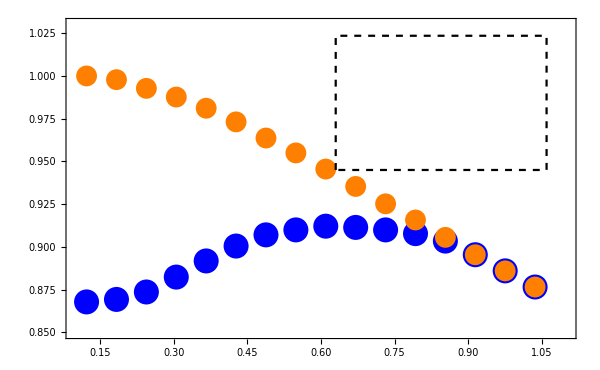

```mathematica
Legended[Show[ListPlot[Transpose@{TempArray/Tc,AvgCurvatureA/Max[AvgCurvatureB]},PlotStyle->{Blue,PointSize[0.03]},PlotRange->{{0.1,1.1},{0.85,1.03}}],ListPlot[Transpose@{TempArray/Tc,AvgCurvatureB/Max[AvgCurvatureB]},PlotStyle->{Orange,PointSize[0.025]},BaseStyle->MaTeX],
ListPlot[{{0.63,0.945},{0.63,1.0235},{1.06,1.0235},{1.06,0.945},{0.63,0.945}},Joined-> True,PlotStyle-> {Black,Dashed}],
Frame->True,FrameLabel->{MaTeX["T/T_c",Magnification->3],MaTeX["\\left \\langle \\frac{\\partial^2 \\epsilon}{\\partial k^2} \\right \\rangle",Magnification->3]},
BaseStyle-> texStyle,FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> 16,RotateLabel-> False,ImageSize->600],Placed[legend,Scaled[{0.75,0.75}]]]
```

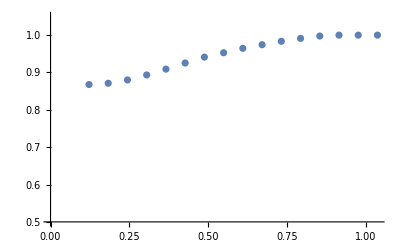

```mathematica
ListPlot[Transpose@{TempArray/Tc,alphaArray},PlotRange->{Automatic,{0.5,1.05}}]
```

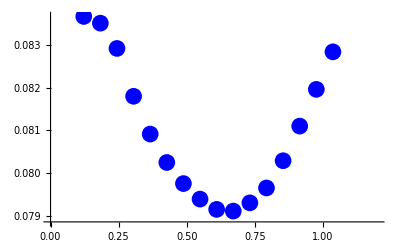

```mathematica
p0=ListPlot[Transpose@{TempArray/Tc,curvxx},PlotStyle->{Blue,PointSize[0.03]},PlotRange->{{0,1.2},Automatic}]
```

```mathematica
displayLaTeX[string_]:=DisplayForm[ToBoxes@TraditionalForm@ToExpression[string,TeXForm,HoldForm]]
```

```mathematica
Min[ρxx]
```

0.0797413

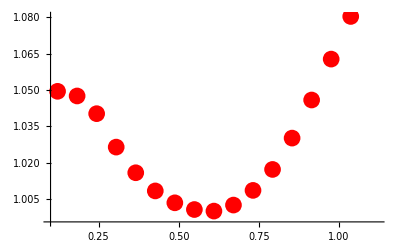

```mathematica
p1=ListPlot[Transpose@{TempArray/Tc,ρxx/Min[ρxx]},PlotStyle->{Red,PointSize[0.03]},PlotRange->{{0.1,1.12},All}]
```

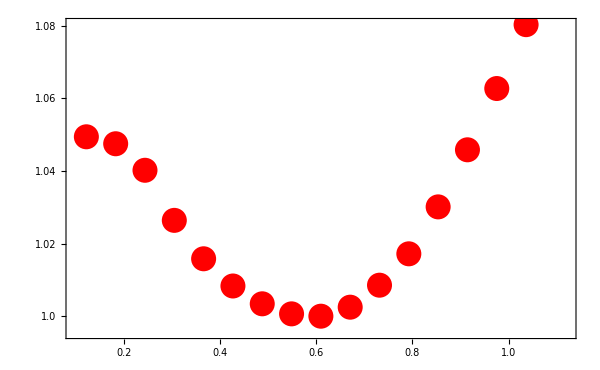

```mathematica
Show[p1,FrameTicks-> {{{{1.0,"1.0"},1.02,1.04,1.06,1.08},None},{{{0.2,"0.2"},{0.4,"0.4"},{0.6,"0.6"},{0.8,"0.8"},{1.0,"1.0"},{1.2,"1.2"}},None}},Frame->True,FrameLabel->{MaTeX["T/T_c",Magnification->3],MaTeX["\\frac{\\rho_{xx}}{\\rho_\\text{Min}}",Magnification->3.5]},BaseStyle-> texStyle,FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> texStyle,RotateLabel-> False,ImageSize->600]
```